## 1. Solving TOV equations.

#### Constants

```mathematica
G = 6.6743 10^-8;
c = 2.99792458 10^10;

Subscript[M, sol]=1.9885 10^33;
α=G Subscript[M, sol]/(10^5 c^2);
Subscript[E0, sol]= Subscript[M, sol] c^2;

mp=1.67262192369 10^-24;
mn=1.67492749804 10^-24;
me = 9.1093837015  10^-28;
c = 2.99792458 10^10;
λp=2.10308910336 10^-14;
λn =2.1001941552  10^-14;
λe = 3.8615926796  10^-11;

km3 = (10.0^5)^3;
rmin = 0.001;
rmax = 350;
densup = 7.86;
```

### 1.1 Equation of state:

#### 1.1.1 Relativistic Case (pure NS)

Let’s try first just this one: relativistic case

```mathematica
Pressure R[ϵ_]:=ϵ/3;
Density R[p_]:=3p;
```

#### 1.1.2 Non Relativistic Case (pure NS)

Pressure and density take the following form

```mathematica
ϵ(P) = 5 (m/(15 π^2 λ^3))^(2/5)P^(3/5)
```

with m, λ of the gas we are considering, let’s say neutrons only, then

```mathematica
kf[m_,l_]:=5((m c^2)/(15 π^2 l^3))^(0.4);
kn=kf[mn,λn];
kp=kf[mp,λp];
ke=kf[me,λe];

Density NR[p_]:=kn p^0.6
```

#### 1.1.3 Whole Range Neutron Star (Pure NS)

We need first to define density and pressure as function of non-dimensional fermi momentum

```mathematica
nfun[m_,l_]:= (m c^2)/(8 π^2 l^3)
epsilon i[z_,m_,l_]:= nfun[m,l]((2 z^3 + z )Sqrt[1 +z^2] - ArcSinh[z])
pressure i[z_,m_,l_]:=nfun[m,l]((2z^3 /3-z)Sqrt[1+z^2]+ArcSinh[z])
```

now, we create a table of data (p, ϵ):

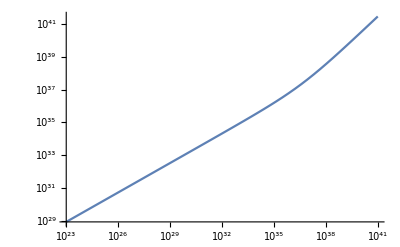

```mathematica
ListEoS n={};
Do[ ListEoS n=Union[ListEoS n,Table[{pressure i[z,mn,λn],epsilon i[z,mn,λn]},{z,10.^i,10^(i+1)-10^(i-1),10^(i-2)}]],{i,-3,2}]
EoS n=Interpolation[ListEoS n,InterpolationOrder->100];LogLogPlot[EoS n[x],{x,10^23,10^41}]
```

Now, let’s build the function for the whole range as a piecewise function taking the R and NR approx,

```mathematica
pw=Piecewise[{{Density NR[x], 0≤  x<10^23}, {EoS n[x],10^23≤ x≤ 10^45},{Density R[x],x>10^45}}];
dener n[p_]:=pw/.x-> p
```

Now we can proceed to do the numerical integration

#### Newton Equations:

We solve first this simple case.

```mathematica
Pc = 3.3 10^34;
ListRG={};
Do[
dener=dener n;
{solutionN = NDSolve[{p'[r]== If[p[r]>0,-(α dener[p[r]*Pc]*M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solutionN[[1]];
pressure ad[x_]:=p[x]/.solutionN[[1]];
If[pressure ad[rad]==0,
Print["Central Pressure = ", Pc, "\n",
	"Radius in km = ", rad, "\n",
	"Mass in M_s = ", mass ad[rad]];
Break[],
ListRG=Append[ListRG,{rad,dener[Pc*pressure ad[rad]]}]
];
},
{rad,1,15,.1}]
```

Central Pressure = 3.3×10^34
Radius in km = 14.8
Mass in M_s = 0.804711

### TOV Equations: Theory

The equations to solve are, in non dimensional form

```mathematica
(d p)/(d r)= -(α [M(r) + β(Pc) r^3 p(r)][ϵ(p(r)) + p(r)][r^2 - 2 α r M(r)])^-1
```

This gives us non dimensional pressure and energy density. Along with the non-dimensional mass, this will be useful to define the metric tensor component functions:

```mathematica
Subscript[g, rr](r)=A(r) = (1 - (2 G M(r))/r)^-1 = (1 - 2α (M̄)/r)^-1
```

with M̄ in units of solar masses and r in km. And the other function comes from the diff. eq.

```mathematica
(B'(r))/(B(r))= - (2 P'(r))/(P(r)+ϵ(r))
```

with boundary conditions in the surface equal to the Schwarzschild solution for the exterior metric.
Given  A=g_rr and B=g_tt, we already have all the components of the metric. The general energy diff. eq. is

```mathematica
1/2(dr/dτ)^2+1/2 g^rr(r)(1 - g^tt(r) E^2)c^2=0
```

from this energy-like equation, consider the potential part, at the turning points (r=R),

```mathematica
V(R) = 1/2 g^rr(R)(1 - g^tt(R) E^2)c^2=0
E^2= 1/(g^tt(R))= Subscript[g, tt](R) 
-> E^2 = B(R)
```

we have therefore the following integral:

```mathematica
Δτ = 2/c∫(√(-Subscript[g, tt](r)))/(√(1 - E^2/Subscript[g, rr](r)))ⅆr
Δτ = 2/c(∫_0)^R(√(A(r)B(r)))/(√(B(R)- B(r)))ⅆr
```

that gives us proper times in seconds.

### TOV Equations : Computation

The following is the code that returns proper times for some NS’s with different central pressures:

#### Gravity Tunnel inside the NS (Pure case)

```mathematica
ListPc ={10.^33,10.^35};
Listϵ={};
Listp={};
ϵ n=Table[0,Length[ListPc]];
p n=Table[0,Length[ListPc]];
Do[{
Pc = ListPc[[ñ]];
Print["NS number ", ñ, " - Central Pressure: ", ScientificForm[Pc]]; 
localp = {};
localϵ = {};
Print["Solving equations..."];

Do[{ 
(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(* Interpolation of solutions*)
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];

(* Integrate until surface *)
If[TOVpressure[rad]==0,
Break[],
localϵ=Append[localϵ,{rad,dener[Pc*TOVpressure[rad]]/Pc}];
localp=Append[localp,{rad,TOVpressure[rad]}];
R=rad;
MStar=mass[rad];
];
},{rad,rmin+0.1,15,.1}];

Print["Equations solved.\n",
	"Radius in km: ", R, "\n",
	"Mass in M_s: ", MStar, "\n"],


ϵ n= Interpolation[localϵ,InterpolationOrder->10];
p n =Interpolation[localp,InterpolationOrder->10];

Print["Finding metric coefficients..."];

A[r_]:= (1 - 2 α mass[r]/r)^-1;
Bmax =1- (2 α)/R;
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] p n'[r]/(p n[r]+ϵ n[r]),Bb[R]== Bmax},Bb[r],{r,rmin+0.1,R}];
B[r_]=Bb[r]/.BFunction[[1]];
Print["Found. \n",
	"Computing times...\n"];
τsNS =2 NIntegrate[Sqrt[A[r] B[r]/(B[R]-B[r])],{r,rmin,R}]/(10^(-5) c);
tsNS =2 NIntegrate[Sqrt[A[r] B[R]/(B[r](B[R]-B[r]))],{r,rmin,R}]/(10^(-5) c);
Print["Proper time in min: ", τsNS/60,"\n",
	"Coordinate time in min: ", tsNS/60, "\n",
"----------------------------------------"]
},{ñ,1,Length[ListPc]}]
```

NS number 1 - Central Pressure: 1.×10^33

Solving equations...

Equations solved.
Radius in km: 14.901
Mass in M_s: 0.243368

Finding metric coefficients...

Found. 
Computing times...

Proper time in min: 0.0000146143
Coordinate time in min: 0.0000166074
----------------------------------------

NS number 2 - Central Pressure: 1.×10^35

Solving equations...

Equations solved.
Radius in km: 11.301
Mass in M_s: 0.674618

Finding metric coefficients...

Found. 
Computing times...

Proper time in min: 5.05583×10^-6
Coordinate time in min: 6.52852×10^-6
----------------------------------------

```mathematica
PureNSDensity=ListLogPlot[Listϵ,Joined->True,
Frame->True,
PlotStyle->Red,
FrameLabel->{"r [km]","ρ(r) [g / cm^3]"}]
```

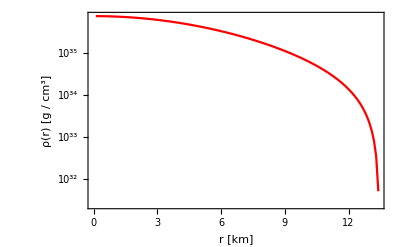

```mathematica
Export["Plots/PureNS_Density.pdf",PureNSDensity];
```

## Equation of state npe

```mathematica
Zp[z_,mn_,mp_,me_]:=Sqrt[(mn^2 (1+z^2) - (me^2 + mp^2))^2-4 mp^2 me^2 ]/(2 mp mn Sqrt[1 + z^2])
Ze[z_,mn_,mp_,me_]:=mp/me Zp[z,mn,mp,me]

epsilon pe[z_]:=  epsilon i[z,mp,λp]+epsilon i[mp/me z, me, λe]
pressure pe[z_]:=pressure i[z,mp,λp]+pressure i[mp/me z ,me,λe]

epsilon npe[z_]:= epsilon i[z,mn,λn]+ epsilon i[Zp[z,939.5,938.2,0.511],mp,λp]+epsilon i[Ze[z,939.5,938.2,0.511], me, λe]
pressure npe[z_]:=pressure i[z,mn,λn]+pressure i[Zp[z,mn,mp,me],mp,λp]+pressure i[mp/me Zp[z,mn,mp,me],me,λe]
```

Non relativistic regime (before z_critical=Zc)

```mathematica
Zc=Zp[0,mn,mp,me]
{pressure pe[Zc],pressure npe[0]}
```

0.0012654

{3.03851×10^24,3.03851×10^24}

```mathematica
eos pe[[-1]]
```

{3.03449×10^24,1.1061×10^28}

```mathematica
eos0[[1]]
```

{3.03851×10^24,1.1278×10^28}

```mathematica
eos pe=Table[{pressure pe[z],epsilon pe[z]},{z,0,Zc,10^-6}];
eos0 =Table[{pressure npe[z],epsilon npe[z]},{z,0,10^-3,10^-6 }];
eos1 =Table[{pressure npe[z],epsilon npe[z]},{z,10^-3,10^-2,10^-5}];
eos2=Table[{pressure npe[z],epsilon npe[z]},{z,10.^-2,10^-1,10^-4}];
eos3=Table[{pressure npe[z],epsilon npe[z]},{z,10.^-1,10^0,10^-3}];
eos4=Table[{pressure npe[z],epsilon npe[z]},{z,10.^0,10^1,10^-2}];
eos5=Table[{pressure npe[z],epsilon npe[z]},{z,10.^1,10^2,10^-1}];
eos6=Table[{pressure npe[z],epsilon npe[z]},{z,10.^2,10^3,10^0}];
eos npe=Union[eos pe,eos0,eos1,eos2,eos3,eos4,eos5,eos6];
```

```mathematica
EoS npe = Interpolation[eos npe,InterpolationOrder->1];
```

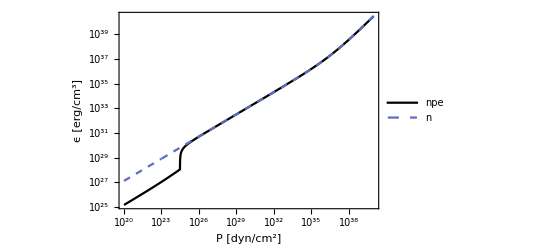

```mathematica
EquationOfState npe = LogLogPlot[{EoS npe[x],dener n[x]},{x,10^20,10^40},
Frame->True,
FrameLabel->{"P [dyn/cm^2]","ϵ [erg/cm^3]"},
PlotStyle->{Black,Dashed},
PlotLegends->Placed[{"npe", "n"},{Left,Top}],
PlotTheme->"Scientific"]
```

```mathematica
Export["Plots/equation_of_state_npe_m.pdf",EquationOfState npe]
```

Plots/equation_of_state_npe_m.pdf